# Mathematica Supplement: Host-parasite genome wide association studies and Coevolutionary simulations.

Keeping pace with the Red Queen: identifying the genetic basis of susceptibility to infectious disease.  Ailene MacPherson, Sarah P. Otto, and Scott L. Nuismer. Genetics.

```mathematica
Clear["Global`*"]
```

We are interested in determining the genetic basis of susceptibility (S) of a host (H) to a parasite (P).  We begin by deriving defining three different functions for the susceptibility as a function of host and pathogen genes. These functional forms include the phentoypic-difference model, the phenotypic matching-model, the 2-locus matching-alleles model

## Defining Interactions: Deriving expressions for S(X_H,X_P)

## Phenotypic-Difference model

We begin by considering a host-parasite interaction which is determined by a phenotype z_H in the host and a phenotype z_P in the pathogen. We begin by considering the phenotypes z_H and z_P have the simplest possible genetic basis for a “complex trait”.  In particular, suppose they are each determined by two additive loci each with two alleles.  If we let X_S[i] be an indicator variable that takes on a value of 0 or 1 depending on the allele present at locus i in species S, and let bSi be the additive effect size of a “1” allele at locus i in species S, we can express the phenotypes of the two species as follows.

```mathematica
zH[XH1_,XH2_]:=bH0+bH1 XH1+bH2 XH2+eH;
zP[XP1_,XP2_]:=bP0+bP1 XP1+bP2 XP2+eP;
```

Here bH0 and bP0 is the phenotype of an individual with both “0” alleles present.

In the difference phenotype model, host susceptibility (probability of infection) is given by the following function of z_H and z_P:

```mathematica
Pdiff[zH_,zP_]:=1/(1+Exp[α (zH-zP)])
```

Assuming that the difference between the host and pathogens phenotypes is small, (zH-zP)≈0, in this case susceptibility can be approximated by the first few terms (2nd order) Taylor series expansion

```mathematica
PdiffA[zH_,zP_]:=Normal[Series[Pdiff[zh,zp]/.{(zh-zp)->x},{x,0,2}]]/.x->(zH-zP)
```

Substituting in zH and zP we have an expression for susceptibility becomes.

```mathematica
PdiffA[zH[XH1,XH2],zP[XP1,XP2]]
```

1/2-1/4 (bH0-bP0+eH-eP+bH1 XH1+bH2 XH2-bP1 XP1-bP2 XP2) α

Finally by letting variable XH be a vector of the host alleles and XP a vector or the pathogen alleles

```mathematica
PdiffX[XH_,XP_]:=PdiffA[zH[XH[[1]],XH[[2]]],zP[XP[[1]],XP[[2]]]]
```

## The Phenotypic-Matching model

As with the phenotypic-difference model we begin by defining a simple genetic architecture to two traits z_H and z_P as a additive function of two loci in the host and two loci in the pathogen respectively.

```mathematica
zH[XH1_,XH2_]:=bH0+bH1 XH1+bH2 XH2+eH;
zP[XP1_,XP2_]:=bP0+bP1 XP1+bP2 XP2+eP;
```

However now susceptibility has a gaussian form:

```mathematica
Pmatch[zH_,zP_]:=Exp[-α (zH-zP)^2]
```

When we approximate this function with the first 2 terms of the Taylor series about (zH-zP)≈0 we have

```mathematica
PmatchA[zH_,zP_]:=Normal[Series[Pmatch[zh,zp]/.{(zh-zp)->x},{x,0,2}]]/.x->(zH-zP)
```

Substituting in zH and zP we have an expression for susceptibility becomes.

```mathematica
PmatchA[zH[XH1,XH2],zP[XP1,XP2]]
```

1-(bH0-bP0+eH-eP+bH1 XH1+bH2 XH2-bP1 XP1-bP2 XP2)^2 α

Finally by letting variable XH be a vector of the host alleles and XP a vector or the pathogen alleles

```mathematica
PmatchX[XH_,XP_]:=PmatchA[zH[XH[[1]],XH[[2]]],zP[XP[[1]],XP[[2]]]]
```

## 2-locus Matching-alleles model

For the final model of susceptibility we use an interaction which is explicitly defined to depend on the combination of host and parasite loci present. In particular for a haploid 2-locus host and parasite each of the four host genotypes can be infected by the corresponding genotype in the pathogen.  We define IM as a infection matrix which gives the probability of host genotype i being infected by pathogen genotype j, in this case it is simply the 4x4 identify matrix.

```mathematica
IM={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
```

The resulting susceptibility of the host genotype given by the vector XH by the pathogen genotype XP is given by:

```mathematica
PmamX[XH_,XP_]:=IM[[1+2XH[[1]]+XH[[2]],1+2XP[[1]]+XP[[2]]]]
```

## Inferring genetic effects: Deriving analytical expressions for βs

Here we use two different genetic association study designs to infer the genetic basis of susceptibility.  In the first design, single-species GWAS, we infer the additive effects and epistatic interaction between the loci of a single species.  We arbitrarily chose to focus on the host in this design.  The second design, the two-species CoGWAS, infers the additive effects and epistatic interactions between the loci of both species including the interactions between host and pathogen loci.  The results attained here are derived analytically and represent the expectations given an infinite sample size. We conclude this section by considering the effect of finite sample sizes.

Single-species (Host-Only) GWAS

## The Linear Regression Model

In the host-only method we fit susceptibility with a the following linear regression.

```mathematica
Pfit1[XH_]:=β0+βH1 XH[[1]]+βH2 XH[[2]]+βH12 XH[[1]] XH[[2]]
```

Here βH1 and βH2 are the inferred additive effects of the “1” allele at host locus 1 and 2 whereas βH[1,2] is the inferred epistatic interaction between the host loci.  Finally, β[0] is the intercept which approximates the phenotype of a host individual with all “0” alleles.

Using least squares regression to fit susceptibility of the form, PinfX, we first calculate the mean squared error.  This requires information on the genetic makeup of the host and pathogen populations.  In particular, suppose that the frequency of the “1” allele at locus i in species S is given by pS[i] and the linkage disequilibrium between the loci in species S is given by LDS.  Assuming Hardy-Weinberg proportions in the host and pathogen the resulting frequency of genotype xh1,xh2 in each species is given by:

```mathematica
FreqH[XH1_,XH2_]:=pH1^XH1(1-pH1)^(1-XH1)pH2^XH2(1-pH2)^(1-XH2)+(-1)^Abs[XH1-XH2] LDH//Simplify
FreqP[XP1_,XP2_]:=pP1^XP1(1-pP1)^(1-XP1)pP2^XP2(1-pP2)^(1-XP2)+(-1)^Abs[XP1-XP2] LDP//Simplify
```

Given these genotype frequencies, if we assume hosts and pathogens come into contact with one another at random and that the probability of infection is given by the function PinfX we can write the mean squared error as:

```mathematica
MSE[PinfX_]:=Sum[FreqH[XH1,XH2]FreqP[XP1,XP2](PinfX[{XH1,XH2},{XP1,XP2}]-Pfit1[{XH1,XH2}])^2,{XH1,0,1},{XH2,0,1},{XP1,0,1},{XP2,0,1}]//Simplify;
```

We can then solve for β0, βH1, βH2, and βH12 by minimizing this error. In other words by solving the following equations for β0,βH1, βH2, and βH12

```mathematica
Equs[PinfX_]:={D[MSE[PinfX],β0]==0,D[MSE[PinfX],βH1]==0,D[MSE[PinfX],βH2]==0,D[MSE[PinfX],βH12]==0};
Vars={β0,βH1,βH2,βH12};
```

## Phenotypic-Difference Model

```mathematica
βHOdiff=Solve[Simplify[Equs[PdiffX]],Vars]//Flatten
```

{β0→1/4 (2-bH0 α+bP0 α-eH α+eP α+bP1 pP1 α+bP2 pP2 α),βH1→-(bH1 α)/4,βH2→-(bH2 α)/4,βH12→0}

Plotting these coefficients as a function of pathogen allele frequency pP1=pP2

```mathematica
pars={α->0.8, LDP->0,bH0->0,bH1->0.5,bH2->0.2,bP0->0,bP1->0.35,bP2->0.5,eH->0.0,eP->0.0,pP1->pP,pP2->pP};
```

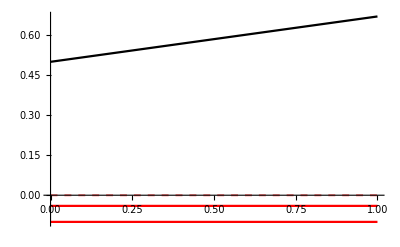

```mathematica
HostOnly=Plot[{β0/.βHOdiff/.pars,βH1/.βHOdiff/.pars,βH2/.βHOdiff/.pars,βH12/.βHOdiff/.pars},{pP,0,1},PlotStyle->{Black,Red,Red,Directive[Pink,Dashed]}]
```

## Phenotypic-Matching Model

```mathematica
βHOmatch=Solve[Simplify[Equs[PmatchX]],Vars]//Flatten
```

{β0→1-bH0^2 α+2 bH0 bP0 α-bP0^2 α-2 bH0 eH α+2 bP0 eH α-eH^2 α+2 bH0 eP α-2 bP0 eP α+2 eH eP α-eP^2 α-2 bP1 bP2 LDP α+2 bH0 bP1 pP1 α-2 bP0 bP1 pP1 α-bP1^2 pP1 α+2 bP1 eH pP1 α-2 bP1 eP pP1 α+2 bH0 bP2 pP2 α-2 bP0 bP2 pP2 α-bP2^2 pP2 α+2 bP2 eH pP2 α-2 bP2 eP pP2 α-2 bP1 bP2 pP1 pP2 α,βH1→-2 bH0 bH1 α-bH1^2 α+2 bH1 bP0 α-2 bH1 eH α+2 bH1 eP α+2 bH1 bP1 pP1 α+2 bH1 bP2 pP2 α,βH2→-2 bH0 bH2 α-bH2^2 α+2 bH2 bP0 α-2 bH2 eH α+2 bH2 eP α+2 bH2 bP1 pP1 α+2 bH2 bP2 pP2 α,βH12→-2 bH1 bH2 α}

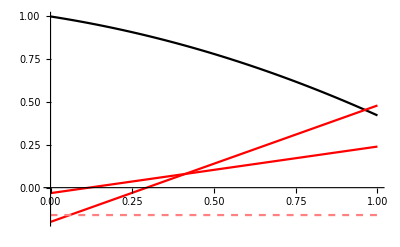

```mathematica
HostOnly=Plot[{β0/.βHOmatch/.pars,βH1/.βHOmatch/.pars,βH2/.βHOmatch/.pars,βH12/.βHOmatch/.pars},{pP,0,1},PlotStyle->{Black,Red,Red,Directive[Pink,Dashed]}]
```

## Matching-Alleles Model

```mathematica
βHOmam=Solve[Simplify[Equs[PmamX]],Vars]//Flatten
```

{β0→1+LDP-pP1-pP2+pP1 pP2,βH1→-1-2 LDP+2 pP1+pP2-2 pP1 pP2,βH2→-1-2 LDP+pP1+2 pP2-2 pP1 pP2,βH12→1+4 LDP-2 pP1-2 pP2+4 pP1 pP2}

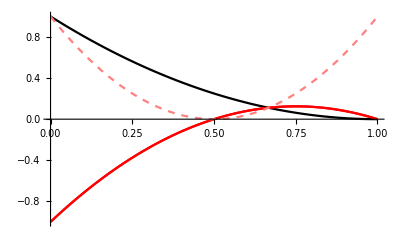

```mathematica
HostOnly=Plot[{β0/.βHOmam/.pars,βH1/.βHOmam/.pars,βH2/.βHOmam/.pars,βH12/.βHOmam/.pars},{pP,0,1},PlotStyle->{Black,Red,Red,Directive[Pink,Dashed]}]
```

Two-species (Host-Pathogen) Co-GWAS

## The Linear Regression Model

In the two-species Co-GWAS method we fit susceptibility with a linear regression containing the additive effects from both species, pair-wise epistatic interactions within each species, and pair-wise GxG interactions between the species.

```mathematica
Pfit2[XH_,XP_]:=β0+βH1 XH[[1]]+βH2 XH[[2]]+βH12 XH[[1]] XH[[2]]+βP1 XP[[1]]+βP2 XP[[2]]+βP12 XP[[1]] XP[[2]]+βH1P1 XH[[1]] XP[[1]]+βH1P2 XH[[1]] XP[[2]]+βH2P1 XH[[2]] XP[[1]]+βH2P2 XH[[2]] XP[[2]]
```

Once again we can use linear least-squares regression to fit susceptibility of the form PinfX.

```mathematica
FreqH[XH1_,XH2_]:=pH1^XH1(1-pH1)^(1-XH1)pH2^XH2(1-pH2)^(1-XH2)+(-1)^Abs[XH1-XH2] LDH//Simplify
FreqP[XP1_,XP2_]:=pP1^XP1(1-pP1)^(1-XP1)pP2^XP2(1-pP2)^(1-XP2)+(-1)^Abs[XP1-XP2] LDP//Simplify
```

```mathematica
MSE2[PinfX_]:=Sum[FreqH[XH1,XH2]FreqP[XP1,XP2](PinfX[{XH1,XH2},{XP1,XP2}]-Pfit2[{XH1,XH2},{XP1,XP2}])^2,{XH1,0,1},{XH2,0,1},{XP1,0,1},{XP2,0,1}]//Simplify;
```

```mathematica
Equs2[PinfX_]:={D[MSE2[PinfX],β0]==0,D[MSE2[PinfX],βH1]==0,D[MSE2[PinfX],βH2]==0,D[MSE2[PinfX],βH12]==0,D[MSE2[PinfX],βP1]==0,D[MSE2[PinfX],βP2]==0,D[MSE2[PinfX],βP12]==0,D[MSE2[PinfX],βH1P1]==0,D[MSE2[PinfX],βH1P2]==0,D[MSE2[PinfX],βH2P1]==0,D[MSE2[PinfX],βH2P2]==0};
Vars2={β0,βH1,βH2,βH12,βP1,βP2,βP12,βH1P1,βH1P2,βH2P1,βH2P2};
```

Since the equations can not be solved directly by Mathematica we use the following list of expressions to solve for the βs step by step.

```mathematica
EquList[PinfX_]:={D[MSE2[PinfX],β0],D[MSE2[PinfX],βH1],D[MSE2[PinfX],βH2],D[MSE2[PinfX],βH12],D[MSE2[PinfX],βP1],D[MSE2[PinfX],βP2],D[MSE2[PinfX],βP12],D[MSE2[PinfX],βH1P1],D[MSE2[PinfX],βH1P2],D[MSE2[PinfX],βH2P1],D[MSE2[PinfX],βH2P2]}
```

## Phenotypic-Difference Model

```mathematica
pars={α->0.8, LDP->0,bH0->0,bH1->0.5,bH2->0.2,bP0->0,bP1->0.35,bP2->0.5,eH->0.0,eP->0.0,pP1->pP,pP2->pP};
```

```mathematica
β0sub=Solve[(EquList[PdiffX][[1]]//Simplify//Factor)==0,β0]//Simplify//Flatten;
```

```mathematica
βH1sub=Solve[(EquList[PdiffX][[2]]/.β0sub//Simplify//Factor)==0,βH1]//Simplify//Flatten;
```

```mathematica
βH2sub=Solve[(EquList[PdiffX][[4]]/.β0sub/.βH1sub//Simplify//Factor)==0,βH2]//Simplify//Flatten;
```

```mathematica
βH12sub=Solve[(EquList[PdiffX][[3]]/.β0sub/.βH1sub/.βH2sub//Simplify//Factor)==0,βH12]//Simplify//Flatten;
```

```mathematica
βP1sub=Solve[(EquList[PdiffX][[5]]/.β0sub/.βH1sub/.βH2sub/.βH12sub//Simplify//Factor)==0,βP1]//Simplify//Flatten;
```

```mathematica
βP2sub=Solve[(EquList[PdiffX][[7]]/.β0sub/.βH1sub/.βH2sub/.βH12sub/.βP1sub//Simplify//Factor)==0,βP2]//Simplify//Flatten;
```

```mathematica
βP12sub=Solve[(EquList[PdiffX][[6]]/.β0sub/.βH1sub/.βH2sub/.βH12sub/.βP1sub/.βP2sub//Simplify//Factor)==0,βP12]//Simplify//Flatten;
```

```mathematica
βH1P1sub=Solve[(EquList[PdiffX][[8]]/.β0sub/.βH1sub/.βH2sub/.βH12sub/.βP1sub/.βP2sub/.βP12sub//Simplify//Factor)==0,βH1P1]//Simplify//Flatten;
```

```mathematica
βH1P2sub=Solve[(EquList[PdiffX][[9]]/.β0sub/.βH1sub/.βH2sub/.βH12sub/.βP1sub/.βP2sub/.βP12sub/.βH1P1sub//Simplify//Factor)==0,βH1P2]//Simplify//Flatten;
```

```mathematica
βH2P1sub=Solve[(EquList[PdiffX][[10]]/.β0sub/.βH1sub/.βH2sub/.βH12sub/.βP1sub/.βP2sub/.βP12sub/.βH1P1sub/.βH1P2sub//Simplify//Factor)==0,βH2P1]//Simplify//Flatten;
```

```mathematica
βH2P2sub=Solve[(EquList[PdiffX][[11]]/.β0sub/.βH1sub/.βH2sub/.βH12sub/.βP1sub/.βP2sub/.βP12sub/.βH1P1sub/.βH1P2sub/.βH2P1sub//Simplify//Factor)==0,βH2P2]//Simplify//Flatten;
```

This gives the following solution:

```mathematica
sol=Vars2/.β0sub/.βH1sub/.βH2sub/.βH12sub/.βP1sub/.βP2sub/.βP12sub/.βH1P1sub/.βH1P2sub/.βH2P1sub/.βH2P2sub//Simplify;
βHPdiff={β0->sol[[1]],βH1-> sol[[2]],βH2->sol[[3]],βH12->sol[[4]],βP1->sol[[5]],βP2->sol[[6]],βP12->sol[[7]],βH1P1->sol[[8]],βH1P2->sol[[9]],βH2P1->sol[[10]],βH2P2->sol[[11]]};
```

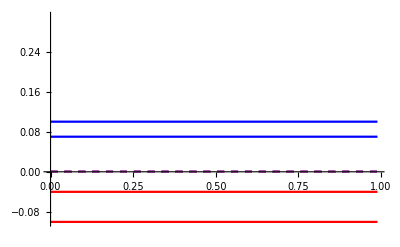

```mathematica
HostPath=Plot[{β0/.βHPdiff/.pars,βH1/.βHPdiff/.pars,βH2/.βHPdiff/.pars,βH12/.βHPdiff/.pars,βP1/.βHPdiff/.pars,βP2/.βHPdiff/.pars,βP12/.βHPdiff/.pars,βH1P1/.βHPdiff/.pars,βH1P2/.βHPdiff/.pars,βH2P1/.βHPdiff/.pars,βH2P2/.βHPdiff/.pars},{pP,0,0.99},PlotStyle->{Black,Red,Red,Directive[Lighter[Red],Dashed],Blue,Blue,Directive[Lighter[Blue],Dashed],Directive[Lighter[Purple],Dashed],Directive[Purple,Dashed],Directive[Lighter[Purple],Dashed],Directive[Lighter[Purple],Dashed]}]
```

## Phenotypic-Matching Model

```mathematica
β0sub=Solve[(EquList[PmatchX][[1]]//Simplify//Factor)==0,β0]//Simplify//Flatten;
```

```mathematica
βH1sub=Solve[(EquList[PmatchX][[2]]/.β0sub//Simplify//Factor)==0,βH1]//Simplify//Flatten;
```

```mathematica
βH2sub=Solve[(EquList[PmatchX][[4]]/.β0sub/.βH1sub//Simplify//Factor)==0,βH2]//Simplify//Flatten;
```

```mathematica
βH12sub=Solve[(EquList[PmatchX][[3]]/.β0sub/.βH1sub/.βH2sub//Simplify//Factor)==0,βH12]//Simplify//Flatten;
```

```mathematica
βP1sub=Solve[(EquList[PmatchX][[5]]/.β0sub/.βH1sub/.βH2sub/.βH12sub//Simplify//Factor)==0,βP1]//Simplify//Flatten;
```

```mathematica
βP2sub=Solve[(EquList[PmatchX][[7]]/.β0sub/.βH1sub/.βH2sub/.βH12sub/.βP1sub//Simplify//Factor)==0,βP2]//Simplify//Flatten;
```

```mathematica
βP12sub=Solve[(EquList[PmatchX][[6]]/.β0sub/.βH1sub/.βH2sub/.βH12sub/.βP1sub/.βP2sub//Simplify//Factor)==0,βP12]//Simplify//Flatten;
```

```mathematica
βH1P1sub=Solve[(EquList[PmatchX][[8]]/.β0sub/.βH1sub/.βH2sub/.βH12sub/.βP1sub/.βP2sub/.βP12sub//Simplify//Factor)==0,βH1P1]//Simplify//Flatten;
```

```mathematica
βH1P2sub=Solve[(EquList[PmatchX][[9]]/.β0sub/.βH1sub/.βH2sub/.βH12sub/.βP1sub/.βP2sub/.βP12sub/.βH1P1sub//Simplify//Factor)==0,βH1P2]//Simplify//Flatten;
```

```mathematica
βH2P1sub=Solve[(EquList[PmatchX][[10]]/.β0sub/.βH1sub/.βH2sub/.βH12sub/.βP1sub/.βP2sub/.βP12sub/.βH1P1sub/.βH1P2sub//Simplify//Factor)==0,βH2P1]//Simplify//Flatten;
```

```mathematica
βH2P2sub=Solve[(EquList[PmatchX][[11]]/.β0sub/.βH1sub/.βH2sub/.βH12sub/.βP1sub/.βP2sub/.βP12sub/.βH1P1sub/.βH1P2sub/.βH2P1sub//Simplify//Factor)==0,βH2P2]//Simplify//Flatten;
```

This gives the following solution:

```mathematica
sol=Vars2/.β0sub/.βH1sub/.βH2sub/.βH12sub/.βP1sub/.βP2sub/.βP12sub/.βH1P1sub/.βH1P2sub/.βH2P1sub/.βH2P2sub//Simplify;
βHPmatch={β0->sol[[1]],βH1-> sol[[2]],βH2->sol[[3]],βH12->sol[[4]],βP1->sol[[5]],βP2->sol[[6]],βP12->sol[[7]],βH1P1->sol[[8]],βH1P2->sol[[9]],βH2P1->sol[[10]],βH2P2->sol[[11]]};
```

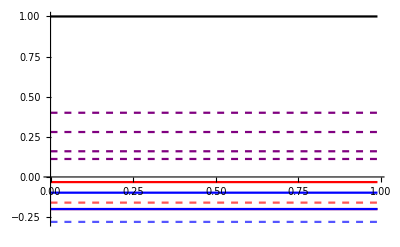

```mathematica
HostPath=Plot[{β0/.βHPmatch/.pars,βH1/.βHPmatch/.pars,βH2/.βHPmatch/.pars,βH12/.βHPmatch/.pars,βP1/.βHPmatch/.pars,βP2/.βHPmatch/.pars,βP12/.βHPmatch/.pars,βH1P1/.βHPmatch/.pars,βH1P2/.βHPmatch/.pars,βH2P1/.βHPmatch/.pars,βH2P2/.βHPmatch/.pars},{pP,0,0.99},PlotStyle->{Black,Red,Red,Directive[Lighter[Red],Dashed],Blue,Blue,Directive[Lighter[Blue],Dashed],Directive[Purple,Dashed],Directive[Purple,Dashed],Directive[Purple,Dashed],Directive[Purple,Dashed]}]
```

## Matching-Alleles Model

```mathematica
βH2P2sub=FullSimplify[Flatten[Solve[EquList[PmamX][[11]]==0,βH2P2]]];
```

```mathematica
βH2P1sub=FullSimplify[Flatten[Solve[Simplify[EquList[PmamX][[3]]/.βH2P2sub]==0,βH2P1]]];
```

```mathematica
βH1sub=FullSimplify[Flatten[Solve[Simplify[EquList[PmamX][[4]]/.βH2P2sub/.βH2P1sub]==0,βH1]]];
```

```mathematica
βH12sub=FullSimplify[Flatten[Solve[Factor[EquList[PmamX][[2]]/.βH2P2sub/.βH2P1sub/.βH1sub]==0,βH12]]];
```

```mathematica
βP2sub=FullSimplify[Flatten[Solve[Factor[EquList[PmamX][[1]]/.βH2P2sub/.βH2P1sub/.βH1sub/.βH12sub]==0,βP2]]];
```

```mathematica
βP1sub=FullSimplify[Flatten[Solve[Factor[EquList[PmamX][[6]]/.βH2P2sub/.βH2P1sub/.βH1sub/.βH12sub/.βP2sub]==0,βP1]]];
```

```mathematica
βH1P2sub=FullSimplify[Flatten[Solve[Factor[EquList[PmamX][[7]]/.βH2P2sub/.βH2P1sub/.βH1sub/.βH12sub/.βP2sub/.βP1sub]==0,βH1P2]]];
```

```mathematica
βP12sub=FullSimplify[Flatten[Solve[Factor[EquList[PmamX][[5]]/.βH2P2sub/.βH2P1sub/.βH1sub/.βH12sub/.βP2sub/.βP1sub/.βH1P2sub]==0,βP12]]];
```

```mathematica
βH1P1sub=FullSimplify[Flatten[Solve[Factor[EquList[PmamX][[9]]/.βH2P2sub/.βH2P1sub/.βH1sub/.βH12sub/.βP2sub/.βP1sub/.βH1P2sub/.βP12sub]==0,βH1P1]]];
```

```mathematica
β0sub=FullSimplify[Flatten[Solve[Factor[EquList[PmamX][[8]]/.βH2P2sub/.βH2P1sub/.βH1sub/.βH12sub/.βP2sub/.βP1sub/.βH1P2sub/.βP12sub/.βH1P1sub]==0,β0]]];
```

```mathematica
βH2sub=FullSimplify[Flatten[Solve[Factor[Simplify[EquList[PmamX][[10]]/.βH2P2sub/.βH2P1sub/.βH1sub/.βH12sub/.βP2sub/.βP1sub/.βH1P2sub/.βP12sub/.βH1P1sub]/.β0sub]==0,βH2]]];
```

```mathematica
sol=Simplify[Vars2/.βH2P2sub/.βH2P1sub/.βH1sub/.βH12sub/.βP2sub/.βP1sub/.βH1P2sub/.βP12sub/.βH1P1sub/.β0sub/.βH2sub];
βHPmam={β0->sol[[1]],βH1->sol[[2]],βH2->sol[[3]],βH12->sol[[4]],βP1->sol[[5]],βP2->sol[[6]],βP12->sol[[7]],βH1P1->sol[[8]],βH1P2->sol[[9]],βH2P1->sol[[10]],βH2P2->sol[[11]]};
```

Unlike the phenotypic-matching and phenotypic-difference model the β coefficients here depend on the host allele frequencies and linkage disequilibrium.

```mathematica
parsH={pH1->0.5,pH2->0.5,LDH->0};
```

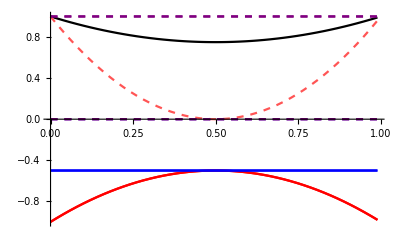

```mathematica
HostPath=Plot[{β0/.βHPmam/.pars/.parsH,βH1/.βHPmam/.pars/.parsH,βH2/.βHPmam/.pars/.parsH,βH12/.βHPmam/.pars/.parsH,βP1/.βHPmam/.pars/.parsH,βP2/.βHPmam/.pars/.parsH,βP12/.βHPmam/.pars/.parsH,βH1P1/.βHPmam/.pars/.parsH,βH1P2/.βHPmam/.pars/.parsH,βH2P1/.βHPmam/.pars/.parsH,βH2P2/.βHPmam/.pars/.parsH},{pP,0,0.99},PlotStyle->{Black,Red,Red,Directive[Lighter[Red],Dashed],Blue,Blue,Directive[Lighter[Blue],Dashed],Directive[Purple,Dashed],Directive[Purple,Dashed],Directive[Purple,Dashed],Directive[Purple,Dashed]}]
```

## Variance explained: Simulating R^2 across pathogen allele frequencies

We begin by constructing a function that simulates a sample of interacting hosts and pathogens given an arbitrary susceptibility function.  We then use this function to simulate samples for each susceptibility function, fit the data with the host only or the two-species model, and calculate the variation explained.

Simulating a sample

For a host a pathogen populations with a particular genetic composition (as specified by the vectors of haplotype frequencies hH and hP) we can simulate a sample of size n.  Given a particular infection model PinfX the following function generates such a sample where column 1: 1 if host is infected 0 if not infected, column 2: allele present at first host locus (XH1), column 3: allele present at second host locus (XH2), column 4: allele present at first parasite locus (XP1), and column 5: allele present at second parasite locus (XP2).

```mathematica
pars2={α->2, LDP->0,bH0->0,bH1->0.5,bH2->0.2,bP0->0,bP1->0.5,bP2->0.35,eH->0.0,eP->0.0};
```

```mathematica
sim[hH_,hP_,n_,PinfX_]:=Block[{rand,rand2,s,out,pinf},out={};
For[s=1,s≤n,s++,
rand=RandomReal[];rand2=RandomReal[];
(*Host and Pathogen Genotypes*)
If[rand<hH[[1]],(*host is 00*) 
If[rand2<hP[[1]],(*path is 00*)AppendTo[out,{0,0,0,0}],
If[rand2<hP[[1]]+hP[[2]],(*path is 01*)AppendTo[out,{0,0,0,1}],
If[rand2<hP[[1]]+hP[[2]]+hP[[3]],(*path is 10*)AppendTo[out,{0,0,1,0}],
(*path is 11*)AppendTo[out,{0,0,1,1}]]]];,
If[rand<hH[[1]]+hH[[2]] ,(*host is 01*)
If[rand2<hP[[1]],(*path is 00*)AppendTo[out,{0,1,0,0}],
If[rand2<hP[[1]]+hP[[2]],(*path is 01*)AppendTo[out,{0,1,0,1}],
If[rand2<hP[[1]]+hP[[2]]+hP[[3]],(*path is 10*)AppendTo[out,{0,1,1,0}],
(*path is 11*)AppendTo[out,{0,1,1,1}]]]];,
If[rand<hH[[1]]+hH[[2]]+hH[[3]],(*host is 10*)
If[rand2<hP[[1]],(*path is 00*)AppendTo[out,{1,0,0,0}],
If[rand2<hP[[1]]+hP[[2]],(*path is 01*)AppendTo[out,{1,0,0,1}],
If[rand2<hP[[1]]+hP[[2]]+hP[[3]],(*path is 10*)AppendTo[out,{1,0,1,0}],
(*path is 11*)AppendTo[out,{1,0,1,1}]]]];,
(*host is 11*)
If[rand2<hP[[1]],(*path is 00*)AppendTo[out,{1,1,0,0}],
If[rand2<hP[[1]]+hP[[2]],(*path is 01*)AppendTo[out,{1,1,0,1}],
If[rand2<hP[[1]]+hP[[2]]+hP[[3]],(*path is 10*)AppendTo[out,{1,1,1,0}],
(*path is 11*)AppendTo[out,{1,1,1,1}]]]];
]]];
(*Host infection Status*)
rand=RandomReal[];
pinf=PinfX[{out[[s,1]],out[[s,2]]},{out[[s,3]],out[[s,4]]}]/.pars2//N;
AppendTo[out[[s]],pinf]
];
out
]
```

Next we construct a function that simulates the data and then fits the data with linear models ranging from a model with only additive host effects through the complete 2 species Co-GWAS. This function outputs a vector of R^2 values for each linear model. The variable x is an arbitrary variable which can be used to used to easily plot the variance explained as quantity “x” changes.  In particular we will use “x”=pathogen allele frequency (x=hP[[3]]+hP[[4]]), and “x”=time (x=t).

```mathematica
SimR2[hH_,hP_,n_,PinfX_,x_]:=Block[{simDat,simDat2,out,lm1,lm2,lm3,lm4,lm5,pP},
simDat=sim[hH,hP,n,PinfX];
(*Fitting additive effects only*)
lm1=LinearModelFit[Transpose[Join[Transpose[simDat[[;;,1;;2]]],{simDat[[;;,5]]}]],{xh1,xh2},{xh1,xh2}];
(*Fitting additive and epistatic effects*)
lm2=LinearModelFit[Transpose[Join[Transpose[simDat[[;;,1;;2]]],{simDat[[;;,1]]*simDat[[;;,2]]},{simDat[[;;,5]]}]],{xh1,xh2,xh12},{xh1,xh2,xh12}];
(*Fitting host-additive, host-epistatic, and parasite-additive effects*)
lm3=LinearModelFit[Transpose[Join[Transpose[simDat[[;;,1;;2]]],{simDat[[;;,1]]*simDat[[;;,2]]},Transpose[simDat[[;;,3;;4]]],{simDat[[;;,5]]}]],{xh1,xh2,xh12,xp1,xp2},{xh1,xh2,xh12,xp1,xp2}];
(*Fitting host-additive, host-epistatic, parasite-additive, and parasite-epistatic effects*)
lm4=LinearModelFit[Transpose[Join[Transpose[simDat[[;;,1;;2]]],{simDat[[;;,1]]*simDat[[;;,2]]},Transpose[simDat[[;;,3;;4]]],{simDat[[;;,3]]*simDat[[;;,4]]},{simDat[[;;,5]]}]],{xh1,xh2,xh12,xp1,xp2,xp12},{xh1,xh2,xh12,xp1,xp2,xp12}];
(*Fitting host-additive, host-epistatic, parasite-additive, and parasite-epistatic effects, GxG interactions*)
lm5=LinearModelFit[Transpose[Join[Transpose[simDat[[;;,1;;2]]],{simDat[[;;,1]]*simDat[[;;,2]]},Transpose[simDat[[;;,3;;4]]],{simDat[[;;,3]]*simDat[[;;,4]]},{simDat[[;;,1]]*simDat[[;;,3]]},{simDat[[;;,1]]*simDat[[;;,4]]},{simDat[[;;,2]]*simDat[[;;,3]]},{simDat[[;;,2]]*simDat[[;;,4]]},{simDat[[;;,5]]}]],{xh1,xh2,xh12,xp1,xp2,xp12,xh1p1,xh1p2,xh2p1,xh2p2},{xh1,xh2,xh12,xp1,xp2,xp12,xh1p1,xh1p2,xh2p1,xh2p2}];
{{x,lm1["RSquared"]},{x,lm2["RSquared"]},{x,lm3["RSquared"]},{x,lm4["RSquared"]},{x,lm5["RSquared"]}}
]
```

Fitting different interaction Models

## Phenotypic-Difference Model

For host haplotype frequencies {0.25,0.25,0.25,0.25} and a sample size of 5000 the parameters given in pars we can simulate model fits as pathogen allele frequency pP1=pP2=pP.

```mathematica
pars
```

{α→0.8,LDP→0,bH0→0,bH1→0.5,bH2→0.2,bP0→0,bP1→0.35,bP2→0.5,eH→0.,eP→0.,pP1→pP,pP2→pP}

```mathematica
VarExp[pP_]:=SimR2[{0.25,0.25,0.25,0.25},{(1-pP)^2+LDP/.pars,(1-pP)pP-LDP/.pars,(1-pP)pP-LDP/.pars,(pP)^2+LDP/.pars},5000,PdiffX,pP]
```

```mathematica
R2table=Table[VarExp[in],{in,0.01,0.99,0.02}];
```

LinearModelFit::rank: The rank of the design matrix 6 is less than the number of terms 7 in the model. The model and results based upon it may contain significant numerical error.

LinearModelFit::rank: The rank of the design matrix 10 is less than the number of terms 11 in the model. The model and results based upon it may contain significant numerical error.

Plotting the variance explained by the host-only model

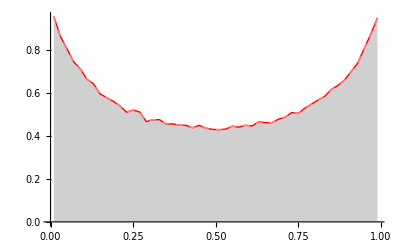

```mathematica
HostOnly=ListLinePlot[{R2table[[;;,1]],R2table[[;;,2]]},PlotStyle->{{Red,Thick},{Pink,Thick,Dashed}},Filling->Axis,FillingStyle->Directive[Gray,Opacity[0.2]]]
```

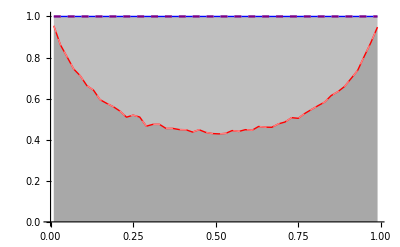

```mathematica
HostPath=ListLinePlot[{R2table[[;;,1]],R2table[[;;,2]],R2table[[;;,3]],R2table[[;;,4]],R2table[[;;,5]]},PlotStyle->{{Red,Thick},{Pink,Thick,Dashed},{Blue,Thick},{LightBlue,Thick,Dashed},{Purple,Dashed}},Filling->Axis,FillingStyle->Directive[Gray,Opacity[0.2]]]
```

## Phenotypic-Matching Model

For host haplotype frequencies {0.25,0.25,0.25,0.25} and a sample size of 5000 the parameters given in pars we can simulate model fits as pathogen allele frequency pP1=pP2=pP.

```mathematica
pars
```

{α→0.8,LDP→0,bH0→0,bH1→0.5,bH2→0.2,bP0→0,bP1→0.35,bP2→0.5,eH→0.,eP→0.,pP1→pP,pP2→pP}

```mathematica
VarExp[pP_]:=SimR2[{0.25,0.25,0.25,0.25},{(1-pP)^2+LDP/.pars,(1-pP)pP-LDP/.pars,(1-pP)pP-LDP/.pars,(pP)^2+LDP/.pars},5000,PmatchX,pP]
```

```mathematica
R2table=Table[VarExp[in],{in,0.01,0.99,0.02}];
```

LinearModelFit::rank: The rank of the design matrix 6 is less than the number of terms 7 in the model. The model and results based upon it may contain significant numerical error.

LinearModelFit::rank: The rank of the design matrix 10 is less than the number of terms 11 in the model. The model and results based upon it may contain significant numerical error.

Plotting the variance explained by the host-only model

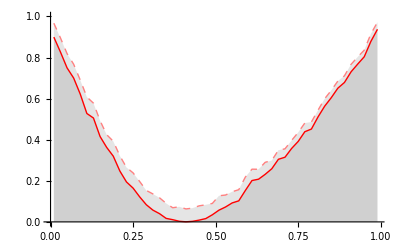

```mathematica
HostOnly=ListLinePlot[{R2table[[;;,1]],R2table[[;;,2]]},PlotStyle->{{Red,Thick},{Pink,Thick,Dashed}},Filling->Axis,FillingStyle->Directive[Gray,Opacity[0.2]],PlotRange->{0,1}]
```

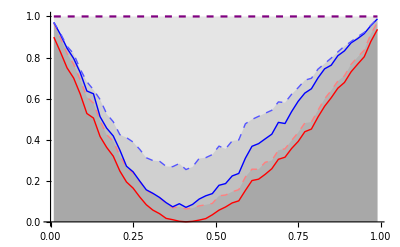

```mathematica
HostPath=ListLinePlot[{R2table[[;;,1]],R2table[[;;,2]],R2table[[;;,3]],R2table[[;;,4]],R2table[[;;,5]]},PlotStyle->{{Red,Thick},{Pink,Thick,Dashed},{Blue,Thick},{Lighter[Blue],Thick,Dashed},{Purple,Dashed}},Filling->Axis,FillingStyle->Directive[Gray,Opacity[0.2]],PlotRange->{0,1}]
```

## Matching-alleles model

For host haplotype frequencies {0.25,0.25,0.25,0.25} and a sample size of 5000 the parameters given in pars we can simulate model fits as pathogen allele frequency pP1=pP2=pP.

```mathematica
pars
```

{α→0.8,LDP→0,bH0→0,bH1→0.5,bH2→0.2,bP0→0,bP1→0.35,bP2→0.5,eH→0.,eP→0.,pP1→pP,pP2→pP}

```mathematica
VarExp[pP_]:=SimR2[{0.25,0.25,0.25,0.25},{(1-pP)^2+LDP/.pars,(1-pP)pP-LDP/.pars,(1-pP)pP-LDP/.pars,(pP)^2+LDP/.pars},5000,PmamX,pP]
```

```mathematica
R2table=Table[VarExp[in],{in,0.01,0.99,0.02}];
```

Plotting the variance explained by the host-only model

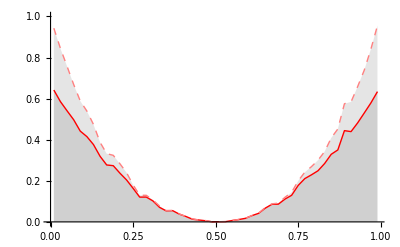

```mathematica
HostOnly=ListLinePlot[{R2table[[;;,1]],R2table[[;;,2]]},PlotStyle->{{Red,Thick},{Pink,Thick,Dashed}},Filling->Axis,FillingStyle->Directive[Gray,Opacity[0.2]],PlotRange->{0,1}]
```

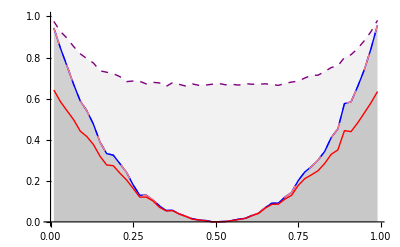

```mathematica
HostPath=ListLinePlot[{R2table[[;;,5]],R2table[[;;,4]],R2table[[;;,3]],R2table[[;;,3]],R2table[[;;,1]]},PlotStyle->{{Purple,Thick,Dashed},{Lighter[Blue],Thick,Dashed},{Blue,Thick},{Pink,Thick,Dashing[{0.03,0.07-0.03}]},{Red,Thick}},Filling->Axis,FillingStyle->Directive[Gray,Opacity[0.1]],PlotRange->{0,1}]
```

## Coevolution: Simulating Coevolution

Phenotypic-difference Model

## Allele Frequencies over time

```mathematica
pars3={tmax->1000,r->0.5,α->0.2,ξH->0.5,ξP->0.5,bH0->0,bH1->3,bH2->2,bP0->0,bP1->4,bP2->1,eH->0.0,eP->0.0,μ->0.001};
```

Here we let the susceptiblity determine the probability of infection of a host with phenotype z_H by a pathogen with phenotype z_P. If infected hosts suffer a fitness cost ξH and pathogens a fitness increase ξP.  Let’s denote the frequency of the host genotype {XH1,XH2} and pathogen genotype {XP1,XP2} in generation t by fH[XH1,XH2,t] and fP[XP1,XP2,t] respectively.  The fitness of the host genotype {XH1,XH2} and pathogen genotype {XP1,XP2} in generation t then is given by:

```mathematica
WH[XH1_,XH2_,t_]:=Sum[fP[XP1,XP2,t](1-ξH Pdiff[zH[XH1,XH2],zP[XP1,XP2]]),{XP1,0,1},{XP2,0,1}]
```

The average host fitness at time t is given by:

```mathematica
WHavg[t_]:=Sum[fH[XH1,XH2,t]WH[XH1,XH2,t],{XH1,0,1},{XH2,0,1}]
```

Hence the relative fitness of host genotype {XH1,XH2} is given by:

```mathematica
wH[XH1_,XH2_,t_]:=WH[XH1,XH2,t]/WHavg[t]
```

Similarly we can calculate the recursion equation for the change in parasite genotype frequencies.  The absolute fitness of genotype {XP1,XP2} is given by

```mathematica
WP[XP1_,XP2_,t_]:=Sum[fH[XH1,XH2,t](1+ξP(Pdiff[zH[XH1,XH2],zP[XP1,XP2]])),{XH1,0,1},{XH2,0,1}]
```

The average pathogen fitness is:

```mathematica
WPavg[t_]:=Sum[fP[XP1,XP2,t]WP[XP1,XP2,t],{XP1,0,1},{XP2,0,1}]
```

The relative fitness

```mathematica
wP[XP1_,XP2_,t_]:=WP[XP1,XP2,t]/WPavg[t]
```

```mathematica
Module[{Htmp,Ptmp,t},ListH={};ListP={};
(*Inializing*)
AppendTo[ListH,{0.24,0.25,0.27,0.24}];
AppendTo[ListP,{0.23,0.25,0.27,0.25}];
For[t=1,t≤ tmax/.pars3,t++,
Htmp={fH[0,0,t] WH[0,0,t]/WHavg[t],fH[1,0,t] WH[1,0,t]/WHavg[t],fH[0,1,t] WH[0,1,t]/WHavg[t],fH[1,1,t] WH[1,1,t]/WHavg[t]}/.{fH[0,0,t]-> ListH[[t,1]],fH[1,0,t]-> ListH[[t,2]],fH[0,1,t]-> ListH[[t,3]],fH[1,1,t]-> ListH[[t,4]]}/.{fP[0,0,t]-> ListP[[t,1]],fP[1,0,t]-> ListP[[t,2]],fP[0,1,t]-> ListP[[t,3]],fP[1,1,t]-> ListP[[t,4]]}/.pars3;
Htmp={Htmp[[1]](Htmp[[1]]+(Htmp[[2]]+Htmp[[3]])+(1-r)Htmp[[4]])+r Htmp[[2]]Htmp[[3]],Htmp[[2]](Htmp[[2]]+(Htmp[[1]]+Htmp[[4]])+(1-r)Htmp[[3]])+r Htmp[[1]]Htmp[[4]],
Htmp[[3]](Htmp[[3]]+(Htmp[[1]]+Htmp[[4]])+(1-r)Htmp[[2]])+r Htmp[[1]]Htmp[[4]],
Htmp[[4]](Htmp[[4]]+(Htmp[[2]]+Htmp[[3]])+(1-r)Htmp[[1]])+r Htmp[[2]]Htmp[[3]]
}/.pars3;
AppendTo[ListH,{(1-μ)^2 Htmp[[1]]+μ(1-μ)Htmp[[2]]+(1-μ)μ Htmp[[3]]+μ^2 Htmp[[4]],μ(1-μ)Htmp[[1]]+(1-μ)^2 Htmp[[2]]+μ^2 Htmp[[3]]+(1-μ)μHtmp[[4]],(1-μ)μHtmp[[1]]+μ^2 Htmp[[2]]+(1-μ)^2 Htmp[[3]]+μ(1-μ)Htmp[[4]],μ^2 Htmp[[1]]+(1-μ)μHtmp[[2]]+μ(1-μ) Htmp[[3]]+(1-μ)^2 Htmp[[4]]}/.pars3];
Ptmp={fP[0,0,t] WP[0,0,t]/WPavg[t],fP[1,0,t] WP[1,0,t]/WPavg[t],fP[0,1,t] WP[0,1,t]/WPavg[t],fP[1,1,t] WP[1,1,t]/WPavg[t]}/.{fH[0,0,t]-> ListH[[t,1]],fH[1,0,t]-> ListH[[t,2]],fH[0,1,t]-> ListH[[t,3]],fH[1,1,t]-> ListH[[t,4]]}/.{fP[0,0,t]-> ListP[[t,1]],fP[1,0,t]-> ListP[[t,2]],fP[0,1,t]-> ListP[[t,3]],fP[1,1,t]-> ListP[[t,4]]}/.pars3;
Ptmp={Ptmp[[1]](Ptmp[[1]]+(Ptmp[[2]]+Ptmp[[3]])+(1-r)Ptmp[[4]])+r Ptmp[[2]]Ptmp[[3]],Ptmp[[2]](Ptmp[[2]]+(Ptmp[[1]]+Ptmp[[4]])+(1-r)Ptmp[[3]])+r Ptmp[[1]]Ptmp[[4]],
Ptmp[[3]](Ptmp[[3]]+(Ptmp[[1]]+Ptmp[[4]])+(1-r)Ptmp[[2]])+r Ptmp[[1]]Ptmp[[4]],
Ptmp[[4]](Ptmp[[4]]+(Ptmp[[2]]+Ptmp[[3]])+(1-r)Ptmp[[1]])+r Ptmp[[2]]Ptmp[[3]]
}/.pars3;
AppendTo[ListP,{(1-μ)^2 Ptmp[[1]]+μ(1-μ)Ptmp[[2]]+(1-μ)μ Ptmp[[3]]+μ^2 Ptmp[[4]],μ(1-μ)Ptmp[[1]]+(1-μ)^2 Ptmp[[2]]+μ^2 Ptmp[[3]]+(1-μ)μ Ptmp[[4]],(1-μ)μ Ptmp[[1]]+μ^2 Ptmp[[2]]+(1-μ)^2 Ptmp[[3]]+μ(1-μ)Ptmp[[4]],μ^2 Ptmp[[1]]+(1-μ)μ Ptmp[[2]]+μ(1-μ) Ptmp[[3]]+(1-μ)^2 Ptmp[[4]]}/.pars3];
];
ListHDiff=Transpose[ListH];
ListPDiff=Transpose[ListP];
pHlist={ListHDiff[[1]]+ListHDiff[[3]],ListHDiff[[2]]+ListHDiff[[4]],ListHDiff[[1]]ListHDiff[[4]]-ListHDiff[[2]]ListHDiff[[3]]};
pPlist={ListPDiff[[1]]+ListPDiff[[3]],ListPDiff[[2]]+ListPDiff[[4]],ListPDiff[[1]]ListPDiff[[4]]-ListPDiff[[2]]ListPDiff[[3]]};
]
```

Plotting the expected values of zH and zP over time.

```mathematica
zHList=Transpose[{Table[t,{t,0,tmax/.pars3}],Sum[ListHDiff[[2XH2+XH1+1]]zH[XH1,XH2],{XH1,0,1},{XH2,0,1}]/.pars3}];
zPList=Transpose[{Table[t,{t,0,tmax/.pars3}],Sum[ListPDiff[[2XP2+XP1+1]]zP[XP1,XP2],{XP1,0,1},{XP2,0,1}]/.pars3}];
```

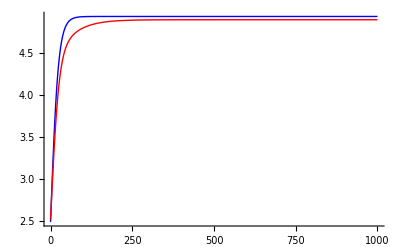

```mathematica
ZPlot=ListLinePlot[{zHList,zPList},PlotRange->All,PlotStyle->{{Blue,Thick},{Red,Thick}}]
```

## Effect Sizes over time

### Host-only GWAS

```mathematica
βHOdiff
```

{β0→1/4 (2-bH0 α+bP0 α-eH α+eP α+bP1 pP1 α+bP2 pP2 α),βH1→-(bH1 α)/4,βH2→-(bH2 α)/4,βH12→0}

```mathematica
PlotHOdiff={Table[{t,β0}/.βHOdiff/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],Table[{t,βH1}/.βHOdiff/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH2}/.βHOdiff/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH12}/.βHOdiff/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}]};
```

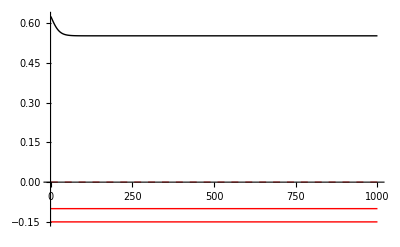

```mathematica
ListLinePlot[PlotHOdiff,PlotStyle->{Directive[{Thick,Black}],Directive[{Thick,Red}],Directive[{Thick,Red}],Directive[{Thick,Lighter[Red],Dashed}]}]
```

### Host-Pathogen Co-GWAS

```mathematica
βHPdiff
```

{β0→1/4 (2-bH0 α+bP0 α-eH α+eP α),βH1→-(bH1 α)/4,βH2→-(bH2 α)/4,βH12→0,βP1→(bP1 α)/4,βP2→(bP2 α)/4,βP12→0,βH1P1→0,βH1P2→0,βH2P1→0,βH2P2→0}

```mathematica
PlotHPdiff={Table[{t,β0}/.βHOdiff/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],Table[{t,βH1}/.βHPdiff/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH2}/.βHPdiff/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH12}/.βHPdiff/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βP1}/.βHPdiff/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βP2}/.βHPdiff/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βP12}/.βHPdiff/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH1P1}/.βHPdiff/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH1P2}/.βHPdiff/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH2P1}/.βHPdiff/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH2P2}/.βHPdiff/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}]};
```

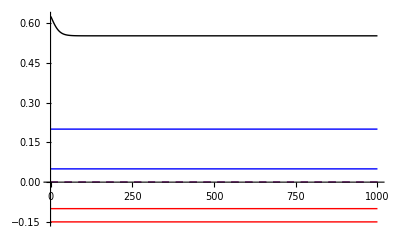

```mathematica
ListLinePlot[PlotHPdiff,PlotStyle->{Directive[{Thick,Black}],Directive[{Thick,Red}],Directive[{Thick,Red}],Directive[{Thick,Lighter[Red],Dashed}],Directive[{Thick,Blue}],Directive[{Thick,Blue}],Directive[{Thick,Lighter[Blue],Dashed}],Directive[{Thick,Lighter[Purple],Dashed}],Directive[{Thick,Lighter[Purple],Dashed}],Directive[{Thick,Lighter[Purple],Dashed}],Directive[{Thick,Lighter[Purple],Dashed}]}]
```

## Variance Explained over time

We can use the sim and SimR2 functions from above.

```mathematica
R2table=Table[SimR2[ListHDiff[[;;,t]],ListPDiff[[;;,t]],1000,PdiffX,t],{t,1,tmax/.pars3,(tmax/.pars3)/100}];
```

LinearModelFit::rank: The rank of the design matrix 3 is less than the number of terms 4 in the model. The model and results based upon it may contain significant numerical error.

LinearModelFit::rank: The rank of the design matrix 5 is less than the number of terms 6 in the model. The model and results based upon it may contain significant numerical error.

LinearModelFit::rank: The rank of the design matrix 6 is less than the number of terms 7 in the model. The model and results based upon it may contain significant numerical error.

General::stop: Further output of LinearModelFit::rank will be suppressed during this calculation.

### Host-only GWAS

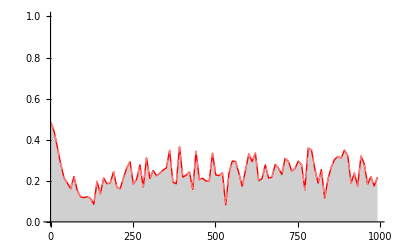

```mathematica
HostOnly=ListLinePlot[{R2table[[;;,1]],R2table[[;;,2]]},PlotStyle->{{Red,Thick},{Pink,Thick,Dashed}},Filling->Axis,FillingStyle->Directive[Gray,Opacity[0.2]],PlotRange->{0,1}]
```

### Host-Pathogen Co-GWAS

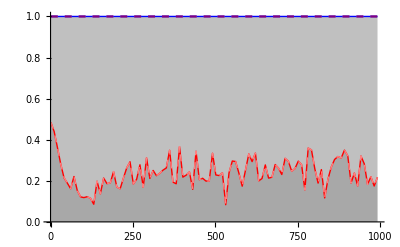

```mathematica
HostPath=ListLinePlot[{R2table[[;;,1]],R2table[[;;,2]],R2table[[;;,3]],R2table[[;;,4]],R2table[[;;,5]]},PlotStyle->{{Red,Thick},{Pink,Thick,Dashed},{Blue,Thick},{Lighter[Blue],Thick,Dashed},{Purple,Dashed}},Filling->Axis,FillingStyle->Directive[Gray,Opacity[0.2]],PlotRange->{0,1}]
```

Phenotypic-matching Model

## Allele Frequencies over time

```mathematica
Pars3={tmax->1000,r->0.5,α->0.2,ξH->0.5,ξP->0.5,bH0->0,bH1->3,bH2->2,bP0->0,bP1->4,bP2->1,eH->0,eP->0,μ->0.001};
```

```mathematica
WH[XH1_,XH2_,t_]:=Sum[fP[XP1,XP2,t](1-ξH Pmatch[zH[XH1,XH2],zP[XP1,XP2]]),{XP1,0,1},{XP2,0,1}]
```

The average host fitness at time t is given by:

```mathematica
WHavg[t_]:=Sum[fH[XH1,XH2,t]WH[XH1,XH2,t],{XH1,0,1},{XH2,0,1}]
```

Hence the relative fitness of host genotype {XH1,XH2} is given by:

```mathematica
wH[XH1_,XH2_,t_]:=WH[XH1,XH2,t]/WHavg[t]
```

Similarly we can calculate the recursion equation for the change in parasite genotype frequencies.  The absolute fitness of genotype {XP1,XP2} is given by

```mathematica
WP[XP1_,XP2_,t_]:=Sum[fH[XH1,XH2,t](1+ξP(Pmatch[zH[XH1,XH2],zP[XP1,XP2]])),{XH1,0,1},{XH2,0,1}]
```

The average pathogen fitness is:

```mathematica
WPavg[t_]:=Sum[fP[XP1,XP2,t]WP[XP1,XP2,t],{XP1,0,1},{XP2,0,1}]
```

The relative fitness

```mathematica
wP[XP1_,XP2_,t_]:=WP[XP1,XP2,t]/WPavg[t]
```

```mathematica
Module[{Htmp,Ptmp,t},ListH={};ListP={};
(*Inializing*)
AppendTo[ListH,{0.24,0.25,0.27,0.24}];
AppendTo[ListP,{0.23,0.25,0.27,0.25}];
For[t=1,t≤ tmax/.pars3,t++,
Htmp={fH[0,0,t] WH[0,0,t]/WHavg[t],fH[1,0,t] WH[1,0,t]/WHavg[t],fH[0,1,t] WH[0,1,t]/WHavg[t],fH[1,1,t] WH[1,1,t]/WHavg[t]}/.{fH[0,0,t]-> ListH[[t,1]],fH[1,0,t]-> ListH[[t,2]],fH[0,1,t]-> ListH[[t,3]],fH[1,1,t]-> ListH[[t,4]]}/.{fP[0,0,t]-> ListP[[t,1]],fP[1,0,t]-> ListP[[t,2]],fP[0,1,t]-> ListP[[t,3]],fP[1,1,t]-> ListP[[t,4]]}/.pars3;
Htmp={Htmp[[1]](Htmp[[1]]+(Htmp[[2]]+Htmp[[3]])+(1-r)Htmp[[4]])+r Htmp[[2]]Htmp[[3]],Htmp[[2]](Htmp[[2]]+(Htmp[[1]]+Htmp[[4]])+(1-r)Htmp[[3]])+r Htmp[[1]]Htmp[[4]],
Htmp[[3]](Htmp[[3]]+(Htmp[[1]]+Htmp[[4]])+(1-r)Htmp[[2]])+r Htmp[[1]]Htmp[[4]],
Htmp[[4]](Htmp[[4]]+(Htmp[[2]]+Htmp[[3]])+(1-r)Htmp[[1]])+r Htmp[[2]]Htmp[[3]]
}/.pars3;
AppendTo[ListH,{(1-μ)^2 Htmp[[1]]+μ(1-μ)Htmp[[2]]+(1-μ)μ Htmp[[3]]+μ^2 Htmp[[4]],μ(1-μ)Htmp[[1]]+(1-μ)^2 Htmp[[2]]+μ^2 Htmp[[3]]+(1-μ)μHtmp[[4]],(1-μ)μHtmp[[1]]+μ^2 Htmp[[2]]+(1-μ)^2 Htmp[[3]]+μ(1-μ)Htmp[[4]],μ^2 Htmp[[1]]+(1-μ)μHtmp[[2]]+μ(1-μ) Htmp[[3]]+(1-μ)^2 Htmp[[4]]}/.pars3];
Ptmp={fP[0,0,t] WP[0,0,t]/WPavg[t],fP[1,0,t] WP[1,0,t]/WPavg[t],fP[0,1,t] WP[0,1,t]/WPavg[t],fP[1,1,t] WP[1,1,t]/WPavg[t]}/.{fH[0,0,t]-> ListH[[t,1]],fH[1,0,t]-> ListH[[t,2]],fH[0,1,t]-> ListH[[t,3]],fH[1,1,t]-> ListH[[t,4]]}/.{fP[0,0,t]-> ListP[[t,1]],fP[1,0,t]-> ListP[[t,2]],fP[0,1,t]-> ListP[[t,3]],fP[1,1,t]-> ListP[[t,4]]}/.pars3;
Ptmp={Ptmp[[1]](Ptmp[[1]]+(Ptmp[[2]]+Ptmp[[3]])+(1-r)Ptmp[[4]])+r Ptmp[[2]]Ptmp[[3]],Ptmp[[2]](Ptmp[[2]]+(Ptmp[[1]]+Ptmp[[4]])+(1-r)Ptmp[[3]])+r Ptmp[[1]]Ptmp[[4]],
Ptmp[[3]](Ptmp[[3]]+(Ptmp[[1]]+Ptmp[[4]])+(1-r)Ptmp[[2]])+r Ptmp[[1]]Ptmp[[4]],
Ptmp[[4]](Ptmp[[4]]+(Ptmp[[2]]+Ptmp[[3]])+(1-r)Ptmp[[1]])+r Ptmp[[2]]Ptmp[[3]]
}/.pars3;
AppendTo[ListP,{(1-μ)^2 Ptmp[[1]]+μ(1-μ)Ptmp[[2]]+(1-μ)μ Ptmp[[3]]+μ^2 Ptmp[[4]],μ(1-μ)Ptmp[[1]]+(1-μ)^2 Ptmp[[2]]+μ^2 Ptmp[[3]]+(1-μ)μ Ptmp[[4]],(1-μ)μ Ptmp[[1]]+μ^2 Ptmp[[2]]+(1-μ)^2 Ptmp[[3]]+μ(1-μ)Ptmp[[4]],μ^2 Ptmp[[1]]+(1-μ)μ Ptmp[[2]]+μ(1-μ) Ptmp[[3]]+(1-μ)^2 Ptmp[[4]]}/.pars3];
];
ListHMatch=Transpose[ListH];
ListPMatch=Transpose[ListP];
]
```

```mathematica
pHlist={ListHMatch[[1]]+ListHMatch[[3]],ListHMatch[[2]]+ListHMatch[[4]],ListHMatch[[1]]ListHMatch[[4]]-ListHMatch[[2]]ListHMatch[[3]]};
pPlist={ListPMatch[[1]]+ListPMatch[[3]],ListPMatch[[2]]+ListPMatch[[4]],ListPMatch[[1]]ListPMatch[[4]]-ListPMatch[[2]]ListPMatch[[3]]};
```

Plotting the expected values of zH and zP over time.

```mathematica
zHList=Transpose[{Table[t,{t,0,tmax/.pars3}],Sum[ListHMatch[[2XH2+XH1+1]]zH[XH1,XH2],{XH1,0,1},{XH2,0,1}]/.pars3}];
zPList=Transpose[{Table[t,{t,0,tmax/.pars3}],Sum[ListPMatch[[2XP2+XP1+1]]zP[XP1,XP2],{XP1,0,1},{XP2,0,1}]/.pars3}];
```

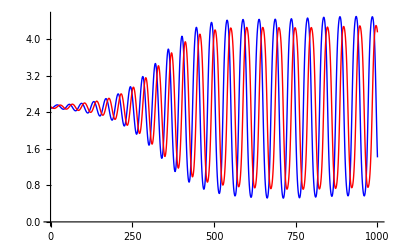

```mathematica
ZPlot=ListLinePlot[{zHList,zPList},PlotRange->All,PlotStyle->{{Blue,Thick},{Red,Thick}}]
```

## Effect Sizes over time

### Host-only GWAS

```mathematica
βHOmatch
```

{β0→1-bH0^2 α+2 bH0 bP0 α-bP0^2 α-2 bH0 eH α+2 bP0 eH α-eH^2 α+2 bH0 eP α-2 bP0 eP α+2 eH eP α-eP^2 α-2 bP1 bP2 LDP α+2 bH0 bP1 pP1 α-2 bP0 bP1 pP1 α-bP1^2 pP1 α+2 bP1 eH pP1 α-2 bP1 eP pP1 α+2 bH0 bP2 pP2 α-2 bP0 bP2 pP2 α-bP2^2 pP2 α+2 bP2 eH pP2 α-2 bP2 eP pP2 α-2 bP1 bP2 pP1 pP2 α,βH1→-2 bH0 bH1 α-bH1^2 α+2 bH1 bP0 α-2 bH1 eH α+2 bH1 eP α+2 bH1 bP1 pP1 α+2 bH1 bP2 pP2 α,βH2→-2 bH0 bH2 α-bH2^2 α+2 bH2 bP0 α-2 bH2 eH α+2 bH2 eP α+2 bH2 bP1 pP1 α+2 bH2 bP2 pP2 α,βH12→-2 bH1 bH2 α}

```mathematica
PlotHOmatch={Table[{t,β0}/.βHOmatch/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],Table[{t,βH1}/.βHOmatch/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH2}/.βHOmatch/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH12}/.βHOmatch/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}]};
```

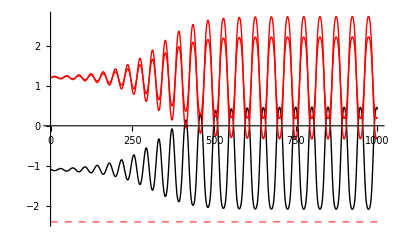

```mathematica
ListLinePlot[PlotHOmatch,PlotStyle->{Directive[{Thick,Black}],Directive[{Thick,Red}],Directive[{Thick,Red}],Directive[{Thick,Lighter[Red],Dashed}]}]
```

### Host-Pathogen Co-GWAS

```mathematica
βHPmatch
```

{β0→1-bH0^2 α-bP0^2 α-eH^2 α+2 bP0 (eH-eP) α+2 eH eP α-eP^2 α+2 bH0 (bP0-eH+eP) α,βH1→-bH1 (2 bH0+bH1-2 (bP0-eH+eP)) α,βH2→-bH2 (2 bH0+bH2-2 (bP0-eH+eP)) α,βH12→-2 bH1 bH2 α,βP1→-bP1 (-2 bH0+2 bP0+bP1-2 eH+2 eP) α,βP2→-bP2 (-2 bH0+2 bP0+bP2-2 eH+2 eP) α,βP12→-2 bP1 bP2 α,βH1P1→2 bH1 bP1 α,βH1P2→2 bH1 bP2 α,βH2P1→2 bH2 bP1 α,βH2P2→2 bH2 bP2 α}

```mathematica
PlotHPmatch={Table[{t,β0}/.βHPmatch/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],Table[{t,βH1}/.βHPmatch/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH2}/.βHPmatch/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH12}/.βHPmatch/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βP1}/.βHPmatch/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βP2}/.βHPmatch/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βP12}/.βHPmatch/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH1P1}/.βHPmatch/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH1P2}/.βHPmatch/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH2P1}/.βHPmatch/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH2P2}/.βHPmatch/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}]};
```

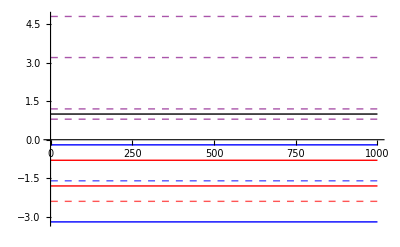

```mathematica
ListLinePlot[PlotHPmatch,PlotStyle->{Directive[{Thick,Black}],Directive[{Thick,Red}],Directive[{Thick,Red}],Directive[{Thick,Lighter[Red],Dashed}],Directive[{Thick,Blue}],Directive[{Thick,Blue}],Directive[{Thick,Lighter[Blue],Dashed}],Directive[{Thick,Lighter[Purple],Dashed}],Directive[{Thick,Lighter[Purple],Dashed}],Directive[{Thick,Lighter[Purple],Dashed}],Directive[{Thick,Lighter[Purple],Dashed}]}]
```

## Variance Explained over time

We can use the sim and SimR2 functions from above.

```mathematica
R2table=Table[SimR2[ListHMatch[[;;,t]],ListHMatch[[;;,t]],1000,PmatchX,t],{t,1,tmax/.pars3,(tmax/.pars3)/100}];
```

### Host-only GWAS

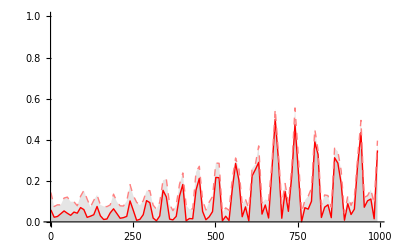

```mathematica
HostOnly=ListLinePlot[{R2table[[;;,1]],R2table[[;;,2]]},PlotStyle->{{Red,Thick},{Pink,Thick,Dashed}},Filling->Axis,FillingStyle->Directive[Gray,Opacity[0.2]],PlotRange->{0,1}]
```

### Host-pathogen Co-GWAS

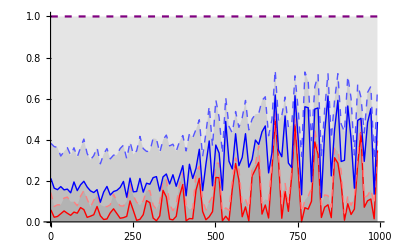

```mathematica
HostPath=ListLinePlot[{R2table[[;;,1]],R2table[[;;,2]],R2table[[;;,3]],R2table[[;;,4]],R2table[[;;,5]]},PlotStyle->{{Red,Thick},{Pink,Thick,Dashed},{Blue,Thick},{Lighter[Blue],Thick,Dashed},{Purple,Dashed}},Filling->Axis,FillingStyle->Directive[Gray,Opacity[0.2]],PlotRange->{0,1}]
```

Matching-alleles Model

## Allele Frequencies over time

```mathematica
Pars3={tmax->1000,r->0.5,α->0.2,ξH->0.5,ξP->0.5,bH0->0,bH1->3,bH2->2,bP0->0,bP1->4,bP2->1,eH->0,eP->0,μ->0.001};
```

```mathematica
WH[XH1_,XH2_,t_]:=Sum[fP[XP1,XP2,t](1-ξH PmamX[{XH1,XH2},{XP1,XP2}]),{XP1,0,1},{XP2,0,1}]
```

The average host fitness at time t is given by:

```mathematica
WHavg[t_]:=Sum[fH[XH1,XH2,t]WH[XH1,XH2,t],{XH1,0,1},{XH2,0,1}]
```

Hence the relative fitness of host genotype {XH1,XH2} is given by:

```mathematica
wH[XH1_,XH2_,t_]:=WH[XH1,XH2,t]/WHavg[t]
```

Similarly we can calculate the recursion equation for the change in parasite genotype frequencies.  The absolute fitness of genotype {XP1,XP2} is given by

```mathematica
WP[XP1_,XP2_,t_]:=Sum[fH[XH1,XH2,t](1+ξP(PmamX[{XH1,XH2},{XP1,XP2}])),{XH1,0,1},{XH2,0,1}]
```

The average pathogen fitness is:

```mathematica
WPavg[t_]:=Sum[fP[XP1,XP2,t]WP[XP1,XP2,t],{XP1,0,1},{XP2,0,1}]
```

The relative fitness

```mathematica
wP[XP1_,XP2_,t_]:=WP[XP1,XP2,t]/WPavg[t]
```

```mathematica
Module[{Htmp,Ptmp,t},ListH={};ListP={};
(*Inializing*)
AppendTo[ListH,{0.24,0.25,0.27,0.24}];
AppendTo[ListP,{0.23,0.25,0.27,0.25}];
For[t=1,t≤ tmax/.pars3,t++,
Htmp={fH[0,0,t] WH[0,0,t]/WHavg[t],fH[1,0,t] WH[1,0,t]/WHavg[t],fH[0,1,t] WH[0,1,t]/WHavg[t],fH[1,1,t] WH[1,1,t]/WHavg[t]}/.{fH[0,0,t]-> ListH[[t,1]],fH[1,0,t]-> ListH[[t,2]],fH[0,1,t]-> ListH[[t,3]],fH[1,1,t]-> ListH[[t,4]]}/.{fP[0,0,t]-> ListP[[t,1]],fP[1,0,t]-> ListP[[t,2]],fP[0,1,t]-> ListP[[t,3]],fP[1,1,t]-> ListP[[t,4]]}/.pars3;
Htmp={Htmp[[1]](Htmp[[1]]+(Htmp[[2]]+Htmp[[3]])+(1-r)Htmp[[4]])+r Htmp[[2]]Htmp[[3]],Htmp[[2]](Htmp[[2]]+(Htmp[[1]]+Htmp[[4]])+(1-r)Htmp[[3]])+r Htmp[[1]]Htmp[[4]],
Htmp[[3]](Htmp[[3]]+(Htmp[[1]]+Htmp[[4]])+(1-r)Htmp[[2]])+r Htmp[[1]]Htmp[[4]],
Htmp[[4]](Htmp[[4]]+(Htmp[[2]]+Htmp[[3]])+(1-r)Htmp[[1]])+r Htmp[[2]]Htmp[[3]]
}/.pars3;
AppendTo[ListH,{(1-μ)^2 Htmp[[1]]+μ(1-μ)Htmp[[2]]+(1-μ)μ Htmp[[3]]+μ^2 Htmp[[4]],μ(1-μ)Htmp[[1]]+(1-μ)^2 Htmp[[2]]+μ^2 Htmp[[3]]+(1-μ)μHtmp[[4]],(1-μ)μHtmp[[1]]+μ^2 Htmp[[2]]+(1-μ)^2 Htmp[[3]]+μ(1-μ)Htmp[[4]],μ^2 Htmp[[1]]+(1-μ)μHtmp[[2]]+μ(1-μ) Htmp[[3]]+(1-μ)^2 Htmp[[4]]}/.pars3];
Ptmp={fP[0,0,t] WP[0,0,t]/WPavg[t],fP[1,0,t] WP[1,0,t]/WPavg[t],fP[0,1,t] WP[0,1,t]/WPavg[t],fP[1,1,t] WP[1,1,t]/WPavg[t]}/.{fH[0,0,t]-> ListH[[t,1]],fH[1,0,t]-> ListH[[t,2]],fH[0,1,t]-> ListH[[t,3]],fH[1,1,t]-> ListH[[t,4]]}/.{fP[0,0,t]-> ListP[[t,1]],fP[1,0,t]-> ListP[[t,2]],fP[0,1,t]-> ListP[[t,3]],fP[1,1,t]-> ListP[[t,4]]}/.pars3;
Ptmp={Ptmp[[1]](Ptmp[[1]]+(Ptmp[[2]]+Ptmp[[3]])+(1-r)Ptmp[[4]])+r Ptmp[[2]]Ptmp[[3]],Ptmp[[2]](Ptmp[[2]]+(Ptmp[[1]]+Ptmp[[4]])+(1-r)Ptmp[[3]])+r Ptmp[[1]]Ptmp[[4]],
Ptmp[[3]](Ptmp[[3]]+(Ptmp[[1]]+Ptmp[[4]])+(1-r)Ptmp[[2]])+r Ptmp[[1]]Ptmp[[4]],
Ptmp[[4]](Ptmp[[4]]+(Ptmp[[2]]+Ptmp[[3]])+(1-r)Ptmp[[1]])+r Ptmp[[2]]Ptmp[[3]]
}/.pars3;
AppendTo[ListP,{(1-μ)^2 Ptmp[[1]]+μ(1-μ)Ptmp[[2]]+(1-μ)μ Ptmp[[3]]+μ^2 Ptmp[[4]],μ(1-μ)Ptmp[[1]]+(1-μ)^2 Ptmp[[2]]+μ^2 Ptmp[[3]]+(1-μ)μ Ptmp[[4]],(1-μ)μ Ptmp[[1]]+μ^2 Ptmp[[2]]+(1-μ)^2 Ptmp[[3]]+μ(1-μ)Ptmp[[4]],μ^2 Ptmp[[1]]+(1-μ)μ Ptmp[[2]]+μ(1-μ) Ptmp[[3]]+(1-μ)^2 Ptmp[[4]]}/.pars3];
];
ListHMAM=Transpose[ListH];
ListPMAM=Transpose[ListP];
]
```

```mathematica
pHlist={ListHMAM[[1]]+ListHMAM[[3]],ListHMAM[[2]]+ListHMAM[[4]],ListHMAM[[1]]ListHMAM[[4]]-ListHMAM[[2]]ListHMAM[[3]]};
pPlist={ListPMAM[[1]]+ListPMAM[[3]],ListPMAM[[2]]+ListPMAM[[4]],ListPMAM[[1]]ListPMAM[[4]]-ListPMAM[[2]]ListPMAM[[3]]};
```

Plotting the allele frequencies over time

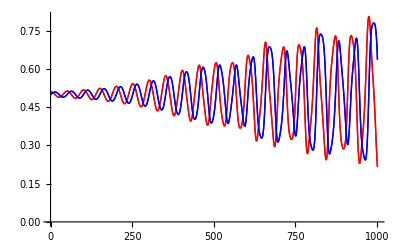

```mathematica
PPlot=ListLinePlot[{pHlist[[1,;;]],pHlist[[1,;;]],pPlist[[1,;;]],pPlist[[1,;;]]},PlotRange->All,PlotStyle->{{Red,Thick},{Red,Thick},{Blue,Thick},{Blue,Thick}}]
```

## Effect Sizes over time

### Host-only GWAS

```mathematica
βHOmam
```

{β0→1+LDP-pP1-pP2+pP1 pP2,βH1→-1-2 LDP+2 pP1+pP2-2 pP1 pP2,βH2→-1-2 LDP+pP1+2 pP2-2 pP1 pP2,βH12→1+4 LDP-2 pP1-2 pP2+4 pP1 pP2}

```mathematica
PlotHOmam={Table[{t,β0}/.βHOmam/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],Table[{t,βH1}/.βHOmam/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH2}/.βHOmam/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH12}/.βHOmam/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]},{t,1,tmax/.pars3}]};
```

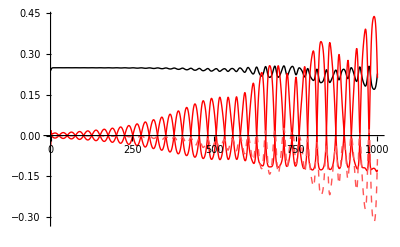

```mathematica
ListLinePlot[PlotHOmam,PlotStyle->{Directive[{Thick,Black}],Directive[{Thick,Red}],Directive[{Thick,Red}],Directive[{Thick,Lighter[Red],Dashed}]}]
```

### Host-Pathogen Co-GWAS

```mathematica
PlotHPmam={Table[{t,β0}/.βHPmam/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]}/.{pH1->pHlist[[1,t]],pH2->pHlist[[2,t]],LDH->pHlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH1}/.βHPmam/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]}/.{pH1->pHlist[[1,t]],pH2->pHlist[[2,t]],LDH->pHlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH2}/.βHPmam/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]}/.{pH1->pHlist[[1,t]],pH2->pHlist[[2,t]],LDH->pHlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH12}/.βHPmam/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]}/.{pH1->pHlist[[1,t]],pH2->pHlist[[2,t]],LDH->pHlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βP1}/.βHPmam/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]}/.{pH1->pHlist[[1,t]],pH2->pHlist[[2,t]],LDH->pHlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βP2}/.βHPmam/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]}/.{pH1->pHlist[[1,t]],pH2->pHlist[[2,t]],LDH->pHlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βP12}/.βHPmam/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]}/.{pH1->pHlist[[1,t]],pH2->pHlist[[2,t]],LDH->pHlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH1P1}/.βHPmam/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]}/.{pH1->pHlist[[1,t]],pH2->pHlist[[2,t]],LDH->pHlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH1P2}/.βHPmam/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]}/.{pH1->pHlist[[1,t]],pH2->pHlist[[2,t]],LDH->pHlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH2P1}/.βHPmam/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]}/.{pH1->pHlist[[1,t]],pH2->pHlist[[2,t]],LDH->pHlist[[3,t]]},{t,1,tmax/.pars3}],
Table[{t,βH2P2}/.βHPmam/.pars3/.{pP1->pPlist[[1,t]],pP2->pPlist[[2,t]],LDP->pPlist[[3,t]]}/.{pH1->pHlist[[1,t]],pH2->pHlist[[2,t]],LDH->pHlist[[3,t]]},{t,1,tmax/.pars3}]};
```

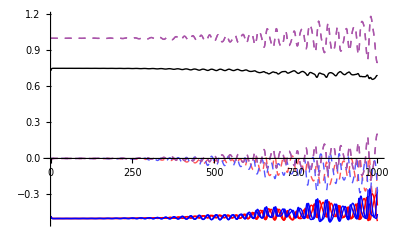

```mathematica
ListLinePlot[PlotHPmam,PlotStyle->{Directive[{Thick,Black}],Directive[{Thick,Red}],Directive[{Thick,Red}],Directive[{Thick,Lighter[Red],Dashed}],Directive[{Thick,Blue}],Directive[{Thick,Blue}],Directive[{Thick,Lighter[Blue],Dashed}],Directive[{Thick,Lighter[Purple],Dashed}],Directive[{Thick,Lighter[Purple],Dashed}],Directive[{Thick,Lighter[Purple],Dashed}],Directive[{Thick,Lighter[Purple],Dashed}]}]
```

## Variance Explained over time

We can use the sim and SimR2 functions from above.

```mathematica
R2table=Table[SimR2[ListHMAM[[;;,t]],ListHMAM[[;;,t]],1000,PmamX,t],{t,1,tmax/.pars3,(tmax/.pars3)/100}];
```

### Host-only GWAS

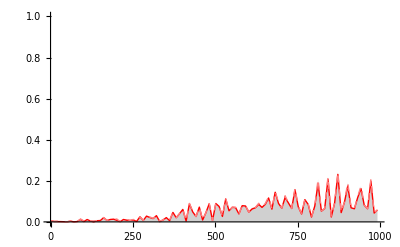

```mathematica
HostOnly=ListLinePlot[{R2table[[;;,1]],R2table[[;;,2]]},PlotStyle->{{Red,Thick},{Pink,Thick,Dashed}},Filling->Axis,FillingStyle->Directive[Gray,Opacity[0.2]],PlotRange->{0,1}]
```

### Host-pathogen Co-GWAS

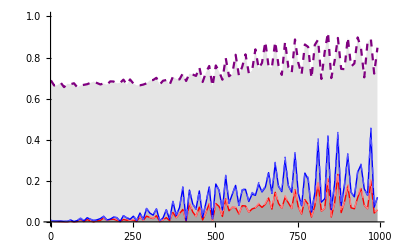

```mathematica
HostPath=ListLinePlot[{R2table[[;;,1]],R2table[[;;,2]],R2table[[;;,3]],R2table[[;;,4]],R2table[[;;,5]]},PlotStyle->{{Red,Thick},{Pink,Thick,Dashed},{Blue,Thick},{Lighter[Blue],Thick,Dashed},{Purple,Dashed}},Filling->Axis,FillingStyle->Directive[Gray,Opacity[0.2]],PlotRange->{0,1}]
```